v2: updated version following notes, plus Mean-field
v3: mean-field (more) + ϵ implementation, bsp

v4: mean-field corrected

### Set Options

Automating good looking plots

```mathematica
SetOptions[ DiscretePlot,Joined-> True, Filling-> None,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium];
SetOptions[ ListPlot,Joined-> True, Filling-> None,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium,PlotStyle->{Black,Thick}];
```

```mathematica
SetOptions[ ListContourPlot,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium]; SetOptions[ ListDensityPlot,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium];
```

```mathematica
SetOptions[ ContourPlot,Frame-> True,LabelStyle->{FontSize->18,FontFamily->"Times",Black},ImageSize->Medium]; SetOptions[ DensityPlot,Frame-> True,LabelStyle->{FontFamily->"CMU Serif",FontSize->24,Black},ImageSize->Medium];
```

### Parameters

Lattice vectors, and basis vectors

```mathematica
a1 = {1,0};a2 ={0,1};τA = {1/2,0};τB = {0,0}; τC = {0,1/2};τvec = {τA,τB, τC};
```

Reciprocal lattice vectors

```mathematica
LatMat = {a1,a2}; 
ReciLatMat = 2π Inverse[LatMat]†;
b1 = ReciLatMat[[1]] ;b2 = ReciLatMat[[2]];
```

```mathematica
δf=N[1/(2√2)];
```

kSpan : set of points for k-sums, and rSpan : set of points for r-sums

```mathematica
kSpan[krange_]:=N[Flatten[Table[i*b1+j*b2,{i,0,0.999,1/krange},{j,0,0.999,1/krange}],1]];
```

```mathematica
rSpan[range_]:=N[Flatten[Table[i*a1+j*a2,{i,-range,range},{j,-range,range}],1]];
```

```mathematica
inp[a_,b_]:= Conjugate[a].b;
```

We will play around with k-range and range to check for convergence

```mathematica
Fermi[β_,x_]:=Chop[N[ 1/(1+ Exp[ β x])]];DFermi[β_,x_] :=D[ Fermi[β,x1],x1]/.{x1-> x};
```

### Bloch Hamiltonian

```mathematica
MatX[λ_,δ_,k_] := Module[ {λR = λ[[1]], λD = λ[[2]],δx = δ[[1]], δy = δ[[2]]}, (1+δx)(IdentityMatrix[2]+ I λR PauliMatrix[2] +I λD PauliMatrix[1]) + (1-δx)Exp[I k.a1](IdentityMatrix[2]- I λR PauliMatrix[2] -I λD PauliMatrix[1])];
```

```mathematica
MatY[λ_,δ_,k_] := Module[ {λR = λ[[1]], λD = λ[[2]],δx = δ[[1]], δy = δ[[2]]}, (1+δy)(IdentityMatrix[2]- I λR PauliMatrix[1] +I λD PauliMatrix[2]) + (1-δy)Exp[I k.a2](IdentityMatrix[2]+ I λR PauliMatrix[1] -I λD PauliMatrix[2])];
```

```mathematica
Clear[hamLieb];hamLieb[bsp_,k_] := hamLieb[bsp,k] = Module[{λ = bsp[[1]], δ = bsp[[2]], ϵ = bsp[[3]]},Module[ {mx = MatX[λ,δ,k],my = MatY[λ,δ,k] },ArrayFlatten[ {{-ϵ IdentityMatrix[2],mx,my},{mx†,0,0},{my†,0,0}} ]]];
```

```mathematica
Block[ {bsp ={RandomReal[{0,1},2],RandomReal[1,2],0.1},k=RandomReal[2π,2]},hamLieb[bsp,k]]//MatrixForm
```

(-0.1 | 0. | 1.69152+0.658 ⅈ | 0.848709+0.0178491 ⅈ | 0.553437+0.678158 ⅈ | 0.78855-1.54387 ⅈ
0. | -0.1 | 0.100854+0.842885 ⅈ | 1.69152+0.658 ⅈ | -1.63886-0.565211 ⅈ | 0.553437+0.678158 ⅈ
1.69152-0.658 ⅈ | 0.100854-0.842885 ⅈ | 0 | 0 | 0 | 0
0.848709-0.0178491 ⅈ | 1.69152-0.658 ⅈ | 0 | 0 | 0 | 0
0.553437-0.678158 ⅈ | -1.63886+0.565211 ⅈ | 0 | 0 | 0 | 0
0.78855+1.54387 ⅈ | 0.553437-0.678158 ⅈ | 0 | 0 | 0 | 0)

```mathematica
Clear[EnerLieb];EnerLieb[bsp_,k_] := EnerLieb[bsp,k]= Chop[  N[Sort[Eigenvalues[hamLieb[bsp,k] ]]] ];
Clear[ULieb];ULieb[bsp_,k_] :=ULieb[bsp,k]=Transpose[Chop[N[   Transpose[ SortBy[ Transpose[ Eigensystem[ hamLieb[bsp,k] ] ] ,First ] ][[2]] ] ] ] ;
```

```mathematica
Block[ {bsp ={RandomReal[{0,1},2],RandomReal[1,2],0.1},k=RandomReal[2π,2]},ULieb[bsp,k]]//MatrixForm
```

(-0.253345+0.434978 ⅈ | 0.487158-0.129294 ⅈ | 0 | 0 | 0.479349-0.127222 ⅈ | -0.249933+0.429119 ⅈ
-0.484614+0.13616 ⅈ | -0.439868-0.246081 ⅈ | 0 | 0 | -0.432817-0.242137 ⅈ | -0.478086+0.134326 ⅈ
-0.128406-0.221877 ⅈ | -0.463199-0.0745519 ⅈ | -0.429662-0.213045 ⅈ | 0.331273+0.282077 ⅈ | 0.470744+0.0757664 ⅈ | 0.13016+0.224906 ⅈ
0.341281-0.288176 ⅈ | 0.0124346+0.174529 ⅈ | -0.34545+0.439321 ⅈ | -0.392981+0.257817 ⅈ | -0.0126372-0.177373 ⅈ | -0.345941+0.292111 ⅈ
0.206791-0.0448018 ⅈ | -0.405312+0.233143 ⅈ | 0.673763-0.0608898 ⅈ | -0.0729731-0.0423247 ⅈ | 0.411915-0.236941 ⅈ | -0.209614+0.0454135 ⅈ
0.428035 | 0.150204 | 0 | 0.763329 | -0.152651 | -0.433879)

#### Plot Band Structure

```mathematica
Gama = {0,0}; Xpoint = b1/2; Mpoint = 1/2(b1+b2);
```

```mathematica
BetAB[ a_, b_] = Table[ (1-i)*a +i*b , {i,0.,1,0.01}];
```

```mathematica
kCut = Join[BetAB[ Gama,Xpoint]  ,BetAB[Xpoint,Mpoint], BetAB[Mpoint,Gama] ];
```

```mathematica
PlotDispData[bsp_] := Table[ EnerLieb[bsp,k]  ,{k,kCut} ];
```

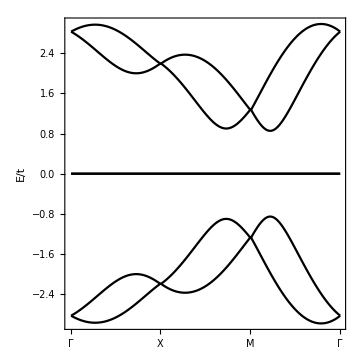

```mathematica
Block[ {bsp={{0.0,0.45},{0.0,0.0},0}},ListPlot[Table[ PlotDispData[bsp][[All,i]],{i,1,6}],PlotStyle->Black,
FrameTicks->{{{1,"Γ"},{101,"X"},{202,"M"},{303,"Γ"}},Automatic},Joined->True,FrameLabel->{None,"E/t"},AspectRatio->1/1]]
```

### Mean Field Theory

Here nup, ndn, splus and sdown are all 3 vectors (for A, B, C)

Follow Eq. 5 of ref https://arxiv.org/pdf/2110.03813.pdf

```mathematica
IJMat[i_,j_]:= ArrayFlatten[ Table[ If[i1==i&&j1==j,1,0],{i1,1,6},{j1,1,6}]];
```

MF vec = { n_(A↑), n_(B↑), n_(C↑), n_(A↓), n_(B↓),n_(C↓), (S^+)_A, (S^+)_B, (S^+)_C, (S^-)_A, (S^-)_B, (S^-)_C}

```mathematica
MFMatvec = {IJMat[2,2],IJMat[4,4], IJMat[6,6], IJMat[1,1],IJMat[3,3], IJMat[5,5], -IJMat[2,1],-IJMat[4,3],-IJMat[6,5],-IJMat[1,2],-IJMat[3,4],-IJMat[5,6]};
```

```mathematica
MFMatvecConj = {IJMat[1,1],IJMat[3,3], IJMat[5,5],IJMat[2,2],IJMat[4,4], IJMat[6,6],-IJMat[1,2],-IJMat[3,4],-IJMat[5,6] , -IJMat[2,1],-IJMat[4,3],-IJMat[6,5]};
```

```mathematica
Clear[HamMFU];HamMFU[MFvec_]:= HamMFU[MFvec] = MFvec.MFMatvec;
```

```mathematica
Clear[HamMFull];HamMFull[bsp_,MFvec_,k_,U_]:= HamMFull[bsp,MFvec,k,U]= hamLieb[bsp,k] +U HamMFU[MFvec];
```

```mathematica
Clear[EnerMF];EnerMF[bsp_,MFvec_,k_,U_] := EnerMF[bsp,MFvec,k,U]= Chop[  N[Sort[Eigenvalues[HamMFull[bsp,MFvec,k,U] ]]] ];
```

```mathematica
Clear[ULiebMF];ULiebMF[bsp_,MFvec_,k_,U_] :=ULiebMF[bsp,MFvec,k,U]=Transpose[Chop[N[   Transpose[ SortBy[ Transpose[ Eigensystem[HamMFull[bsp,MFvec,k,U]  ] ] ,First ] ][[2]] ] ] ] ;
```

```mathematica
Clear[MFvalue];MFvalue[bsp_,MFvec_,U_,μ_,β_,krange_] :=MFvalue[bsp,MFvec,U,μ,β,krange]=Table[1/Length[kSpan[krange]] Sum[ Module[{um = ULiebMF[bsp,MFvec,k,U]}, Fermi[β, EnerMF[bsp,MFvec,k,U][[band]] -μ](um†.MFMatvecConj[[mfvectors]].um)[[band,band]]],{band,1 ,6},{k,kSpan[krange]}],{mfvectors,1,12}];
```

```mathematica
Clear[NumEq];NumEq[bsp_,MFvec_,U_,μ_,β_,krange_] :=NumEq[bsp,MFvec,U,μ,β,krange]=1/Length[kSpan[krange]] Sum[ Fermi[β, EnerMF[bsp,MFvec,k,U][[band]] -μ],{band,1 ,6},{k,kSpan[krange]}];
```

```mathematica
Clear[FindMu];FindMu[bsp_,MFvec_,U_,fil_,β_,krange_] :=FindMu[bsp,MFvec,U,fil,β,krange]=μ/.FindRoot[ NumEq[bsp,MFvec,U,μ,β,krange]-fil,{μ,-10RandomReal[],10RandomReal[]},Evaluated->False, MaxIterations->20,PrecisionGoal->3];
```

```mathematica
Clear[ItrFnMF];ItrFnMF[bsp_,U_,fil_,β_,krange_]:= ItrFnMF[bsp,U,fil,β,krange]=  NestList[ {FindMu[bsp,#[[2]],U,fil,β,krange],MFvalue[bsp,#[[2]],U,#[[1]],β,krange]}&,{RandomReal[],RandomReal[1,12]},10][[10]];
```

```mathematica
Clear[ItrFnMFCheck];ItrFnMFCheck[bsp_,U_,fil_,β_,krange_]:= ItrFnMFCheck[bsp,U,fil,β,krange]=  NestList[ {FindMu[bsp,#[[2]],U,fil,β,krange],MFvalue[bsp,#[[2]],U,#[[1]],β,krange]}&,{RandomReal[],RandomReal[1,12]},10];
```

#### Checks

```mathematica
Block[{bsp={{0.45,0},{0.0,0.0},0.6},U=3,fil=3.0, β=100, krange=30},Module[{itr=ItrFnMFCheck[bsp,U,fil,β,krange]},itr]]
```

{{0.940846,{0.375606,0.280473,0.643642,0.01921,0.891787,0.0997405,0.471254,0.437315,0.602247,0.115279,0.583627,0.1124}},{0.808664-4.71041×10^-15 ⅈ,{0.499266-1.91042×10^-17 ⅈ,0.229548-8.10397×10^-18 ⅈ,0.541099-2.19023×10^-17 ⅈ,0.706483-1.14191×10^-17 ⅈ,0.572917-9.60332×10^-18 ⅈ,0.512769-2.66779×10^-17 ⅈ,-0.152341+7.27813×10^-18 ⅈ,-0.292772-5.72459×10^-19 ⅈ,-0.396175+3.14178×10^-17 ⅈ,-0.15242+1.73627×10^-17 ⅈ,-0.292584+1.84382×10^-17 ⅈ,-0.396272+2.39777×10^-17 ⅈ}},{1.27506+1.05619×10^-18 ⅈ,{0.442761-4.49609×10^-16 ⅈ,0.347691-6.89914×10^-16 ⅈ,0.452842-2.72106×10^-16 ⅈ,0.511769-4.59305×10^-16 ⅈ,0.586359-6.19146×10^-16 ⅈ,0.426682-2.23142×10^-16 ⅈ,-0.0141171+4.09601×10^-16 ⅈ,0.244931-1.81026×10^-16 ⅈ,0.29295+5.07243×10^-17 ⅈ,-0.0141193+3.66569×10^-16 ⅈ,0.244906-2.25562×10^-16 ⅈ,0.292953+6.76995×10^-17 ⅈ}},{1.20992-3.83947×10^-15 ⅈ,{0.567051+9.3728×10^-17 ⅈ,0.3554+1.45535×10^-16 ⅈ,0.48437+3.88317×10^-17 ⅈ,0.57719+1.19747×10^-16 ⅈ,0.573601+2.33376×10^-16 ⅈ,0.472+6.6154×10^-17 ⅈ,0.0842464+1.55222×10^-16 ⅈ,-0.271593-1.09796×10^-16 ⅈ,-0.289788-9.72431×10^-19 ⅈ,0.0842464-1.65537×10^-16 ⅈ,-0.271589-7.91692×10^-18 ⅈ,-0.289788-5.19141×10^-17 ⅈ}},{1.29585+1.03483×10^-15 ⅈ,{0.53739-2.08622×10^-16 ⅈ,0.37558-2.54866×10^-16 ⅈ,0.476319-9.12435×10^-17 ⅈ,0.524942-1.65023×10^-16 ⅈ,0.577598-3.09883×10^-16 ⅈ,0.478094-4.63225×10^-17 ⅈ,-0.117879+1.31441×10^-16 ⅈ,0.294078-2.41732×10^-17 ⅈ,0.294711+3.80163×10^-17 ⅈ,-0.117879+5.80605×10^-18 ⅈ,0.294077-2.29823×10^-16 ⅈ,0.294711-2.33324×10^-17 ⅈ}},{1.25271,{0.565292+7.82186×10^-17 ⅈ,0.38412+8.03884×10^-17 ⅈ,0.467717+2.02913×10^-17 ⅈ,0.543877+8.46829×10^-17 ⅈ,0.572308+1.12783×10^-16 ⅈ,0.480943+3.19523×10^-17 ⅈ,0.135184+1.08503×10^-17 ⅈ,-0.31131-1.45683×10^-16 ⅈ,-0.300092-2.95572×10^-17 ⅈ,0.135184-5.70761×10^-18 ⅈ,-0.31131+8.13022×10^-17 ⅈ,-0.300092+5.44162×10^-19 ⅈ}},{1.28364,{0.554112-8.88007×10^-18 ⅈ,0.391926-8.34628×10^-18 ⅈ,0.46797-1.96574×10^-18 ⅈ,0.529106-8.92327×10^-18 ⅈ,0.564351-1.31803×10^-17 ⅈ,0.489345-1.39466×10^-18 ⅈ,-0.146635-2.17359×10^-17 ⅈ,0.319808+1.19165×10^-16 ⅈ,0.303543-7.12131×10^-18 ⅈ,-0.146635+2.88291×10^-17 ⅈ,0.319808-1.38658×10^-16 ⅈ,0.303543+5.95522×10^-18 ⅈ}},{1.24633,{0.561676+5.03216×10^-20 ⅈ,0.40046-4.01273×10^-20 ⅈ,0.462368-2.19521×10^-20 ⅈ,0.535976+1.50335×10^-19 ⅈ,0.559388+1.64088×10^-19 ⅈ,0.489219+7.36626×10^-20 ⅈ,0.153076+2.34427×10^-17 ⅈ,-0.326551-1.19204×10^-16 ⅈ,-0.305585+2.28296×10^-17 ⅈ,0.153076-2.27577×10^-17 ⅈ,-0.326551+1.19356×10^-16 ⅈ,-0.305585-2.28987×10^-17 ⅈ}},{1.25271,{0.556323+0. ⅈ,0.405855+0. ⅈ,0.462598+0. ⅈ,0.530704+0. ⅈ,0.5507+0. ⅈ,0.492781+0. ⅈ,-0.155993-3.99109×10^-17 ⅈ,0.329125+1.07023×10^-16 ⅈ,0.307146-1.10451×10^-17 ⅈ,-0.155993+3.99109×10^-17 ⅈ,0.329125-1.07023×10^-16 ⅈ,0.307146+1.10451×10^-17 ⅈ}},{1.24263,{0.558284+0. ⅈ,0.412547+0. ⅈ,0.460355+0. ⅈ,0.533486+0. ⅈ,0.545041+0. ⅈ,0.492266+0. ⅈ,0.157536+3.48753×10^-18 ⅈ,-0.331471-1.05043×10^-16 ⅈ,-0.30778+3.89136×10^-17 ⅈ,0.157536-3.48753×10^-18 ⅈ,-0.331471+1.05043×10^-16 ⅈ,-0.30778-3.89136×10^-17 ⅈ}},{1.24507,{0.556116+0. ⅈ,0.417865+0. ⅈ,0.460791+0. ⅈ,0.532447+0. ⅈ,0.539005+0. ⅈ,0.493331+0. ⅈ,-0.158326-3.27213×10^-17 ⅈ,0.33278+9.88815×10^-17 ⅈ,0.308217-3.62407×10^-17 ⅈ,-0.158326+3.27213×10^-17 ⅈ,0.33278-9.88815×10^-17 ⅈ,0.308217+3.62407×10^-17 ⅈ}}}

### Renormalized MF dispersion

```mathematica
Clear[MFEn];MFEn[ bsp_,U_,fil_,β_,k_,krange_]:= MFEn[bsp,U,fil,β,k,krange]= Module[{itr=ItrFnMF[bsp,U,fil,β,krange]}, EnerMF[bsp,itr[[2]],k,U]-itr[[1]]];
```

```mathematica
Clear[MFMass];MFMass[ bsp_,U_,fil_,β_,krange_]:= MFMass[bsp,U,fil,β,krange]= Module[{itr=ItrFnMF[bsp,U,fil,β,krange]}, HamMFU[itr[[2]]] ];
```

```mathematica
Block[ {bsp={{0.5,0.0},{0.0,0.0},0.1},U=1, fil=2.5, β=100,krange=25}, MFMass[bsp,U,fil,β,krange]]//MatrixForm//Chop
```

General::munfl: 2.276168741468×10^-310 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 9.619025505893×10^-312 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 6.751130482434×10^-312 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

(0.470944 | -2.62856×10^-6 | 0 | 0 | 0 | 0
-2.62856×10^-6 | 0.470944 | 0 | 0 | 0 | 0
0 | 0 | 0.764529 | 5.50244×10^-7 | 0 | 0
0 | 0 | 5.50244×10^-7 | 0.764529 | 0 | 0
0 | 0 | 0 | 0 | 0.764528 | 2.53179×10^-6
0 | 0 | 0 | 0 | 2.53179×10^-6 | 0.764526)

```mathematica
Gama = {0,0}; Xpoint = b1/2; Mpoint = 1/2(b1+b2);
```

```mathematica
BetAB[ a_, b_] = Table[ (1-i)*a +i*b , {i,0.,1,0.01}];
```

```mathematica
kCut = Join[BetAB[ Gama,Xpoint]  ,BetAB[Xpoint,Mpoint], BetAB[Mpoint,Gama] ];
```

```mathematica
Clear[PlotMFDisp];PlotMFDisp[bsp_,U_,fil_,β_,krange_] := PlotMFDisp[bsp,U,fil,β,krange]=Table[ MFEn[bsp,U,fil,β,k,krange]  ,{k,kCut} ];
```

General::munfl: 4.193560283706×10^-310 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.890907771237×10^-312 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 3.565206417693×10^-313 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

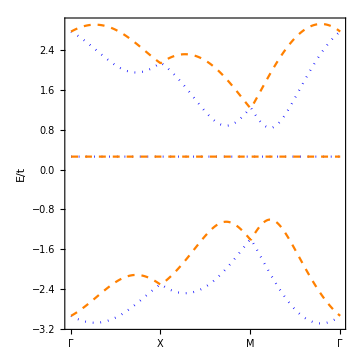

```mathematica
Block[ {bsp={{0.45,0.0},{0.0,0.0},0.6},U=0.5, fil=3.0, β=100,krange=25},ListPlot[Table[ PlotMFDisp[bsp,U,fil,β,krange][[All,i]],{i,1,6,1}],PlotStyle->{{Blue,Dotted},{Orange,Dashed}},
FrameTicks->{{{1,"Γ"},{101,"X"},{202,"M"},{303,"Γ"}},Automatic},Joined->True,FrameLabel->{None,"E/t"},AspectRatio->1/1]]
```

### Mean-Field Magnetization

```mathematica
Clear[Magn];Magn[bsp_,U_, fil_,β_,krange_,orb_]:= Magn[bsp,U,fil,β,krange,orb]=  Module[{itrMF=ItrFnMF[bsp,U,fil,β,krange][[2]]},{1/2( itrMF[[orb+6]] + itrMF[[orb+9]]),1/(2I)( itrMF[[orb+6]] - itrMF[[orb+9]]), 1/2( itrMF[[orb+3]] - itrMF[[orb]])}];
```

```mathematica
Clear[Density];Density[bsp_,U_, fil_,β_,krange_]:= Density[bsp,U,fil,β,krange]=  Module[{itrMF=ItrFnMF[bsp,U,fil,β,krange][[2]]},Total[ itrMF[[1;;6]]] ];
```

```mathematica
Block[ {bsp={{0.45,0.0},{0.0,0.0},0.6},fil=3.0, β=100, krange=30},DiscretePlot[Density[bsp,U,fil,β,krange],{U,0,10},PlotRange->All]]
```

$Aborted

```mathematica
Rasterize[Block[ {bsp={{0.45,0.0},{0.0,0.0},0.6},fil=3.0, β=100, krange=30},DiscretePlot[{Norm[Magn[bsp,U,fil,β,krange,1]],Norm[Magn[bsp,U,fil,β,krange,2]],Norm[Magn[bsp,U,fil,β,krange,3]]},{U,0,10,0.1},PlotRange->All,PlotMarkers->Automatic,Joined->False, PlotLegends->{"<S_A>","<S_B>","<S_C>"},FrameLabel->{"U/t","<S>"}]],ImageResolution->300]
```

-Graphics-

```mathematica
Block[ {bsp={{0.45,0.0},{0.0,0.0},0.6},fil=3.0, β=100, krange=30},Table[{U,Norm[Magn[bsp,U,fil,β,krange,1]],Norm[Magn[bsp,U,fil,β,krange,2]],Norm[Magn[bsp,U,fil,β,krange,3]]},{U,0,10,0.1}]]
```

{{0.,1.26987×10^-16,8.38511×10^-17,1.13802×10^-16},{0.1,1.52298×10^-13,7.16175×10^-13,6.4452×10^-13},{0.2,1.54096×10^-13,2.31842×10^-13,1.99378×10^-13},{0.3,9.45221×10^-11,1.96201×10^-10,5.96432×10^-11},{0.4,5.30702×10^-10,6.5183×10^-10,7.10283×10^-10},{0.5,3.50331×10^-10,3.74774×10^-10,5.49581×10^-10},{0.6,1.32024×10^-9,1.10087×10^-9,1.20912×10^-9},{0.7,7.80944×10^-8,4.68567×10^-8,1.1683×10^-7},{0.8,1.81689×10^-8,1.18451×10^-8,2.12413×10^-8},{0.9,0.0197862,0.237844,0.221782},{1.,7.01482×10^-8,4.81021×10^-8,1.01724×10^-7},{1.1,0.0000140608,0.0000160271,3.8372×10^-6},{1.2,0.0295793,0.249382,0.230346},{1.3,0.0332153,0.253242,0.233716},{1.4,6.38015×10^-7,8.25901×10^-7,9.73231×10^-8},{1.5,0.0000205605,5.4199×10^-6,0.000019233},{1.6,0.0000932686,0.0000277572,0.0000668849},{1.7,0.0500761,0.266625,0.246726},{1.8,4.69204×10^-6,3.75613×10^-6,1.6908×10^-6},{1.9,0.0595442,0.273761,0.254314},{2.,0.0668117,0.280695,0.258342},{2.1,0.0722251,0.283778,0.262612},{2.2,0.0000497053,0.0000289746,0.0000201575},{2.3,0.000132799,0.0000623743,0.0000661285},{2.4,0.000103325,0.0000318847,0.0000723155},{2.5,0.000064979,0.00001469,0.0000427863},{2.6,0.000169838,0.0000584006,0.0000885528},{2.7,0.12263,0.316346,0.290705},{2.8,0.127111,0.312325,0.296678},{2.9,0.0186693,0.0033196,0.00367133},{3.,0.00682803,0.0011455,0.00109346},{3.1,0.0000489351,8.99337×10^-7,1.7567×10^-6},{3.2,6.7285×10^-16,5.80178×10^-17,2.22436×10^-16},{3.3,0.202368,0.358965,0.329967},{3.4,0.174267,0.341621,0.331138},{3.5,0.227003,0.374956,0.341003},{3.6,0.00896883,0.00223667,0.00347756},{3.7,0.0539323,0.0155012,0.0167777},{3.8,0.,0.,0.},{3.9,0.,0.,0.},{4.,0.,0.,0.},{4.1,0.282491,0.400127,0.375802},{4.2,0.287797,0.397484,0.382612},{4.3,0.0277274,0.00193871,0.00302666},{4.4,0.274779,0.394655,0.376547},{4.5,0.319858,0.0267123,0.0351092},{4.6,0.318758,0.416691,0.397578},{4.7,0.,0.,0.},{4.8,0.,0.,0.},{4.9,0.0602177,0.42505,0.433497},{5.,0.,0.,0.},{5.1,0.0531312,0.43076,0.439164},{5.2,0.0680601,0.441325,0.45102},{5.3,0.345108,0.427886,0.413963},{5.4,0.,0.,0.},{5.5,0.,0.,0.},{5.6,0.0613578,0.451399,0.458385},{5.7,0.,0.,0.},{5.8,0.0354004,0.448993,0.45113},{5.9,0.0551401,0.456395,0.461874},{6.,0.,0.,0.},{6.1,0.0385348,0.456524,0.458587},{6.2,0.,0.,0.},{6.3,0.,0.,0.},{6.4,0.,0.,0.},{6.5,0.0466486,0.465172,0.468483},{6.6,0.,0.,0.},{6.7,0.,0.,0.},{6.8,0.0362552,0.466649,0.469522},{6.9,0.,0.,0.},{7.,0.,0.,0.},{7.1,0.0383532,0.470989,0.473249},{7.2,0.0317257,0.47839,0.479733},{7.3,0.,0.,0.},{7.4,0.0362733,0.473789,0.475501},{7.5,0.,0.,0.},{7.6,0.,0.,0.},{7.7,0.,0.,0.},{7.8,0.0207185,0.000537182,0.332453},{7.9,0.,0.,0.},{8.,0.023253,0.482416,0.48273},{8.1,0.,0.,0.},{8.2,0.,0.,0.},{8.3,0.,0.,0.},{8.4,0.491762,0.492804,0.498472},{8.5,0.0171032,0.473808,0.477122},{8.6,0.0274695,0.481063,0.482084},{8.7,0.,0.,0.},{8.8,0.457302,0.475212,0.480591},{8.9,0.,0.,0.},{9.,0.0192263,0.476623,0.48176},{9.1,0.0183783,0.475281,0.481896},{9.2,0.,0.,0.},{9.3,0.,0.,0.},{9.4,0.,0.,0.},{9.5,0.,0.,0.},{9.6,0.,0.,0.},{9.7,0.,0.,0.},{9.8,0.0202068,0.485572,0.486147},{9.9,0.,0.,0.},{10.,0.,0.,0.}}

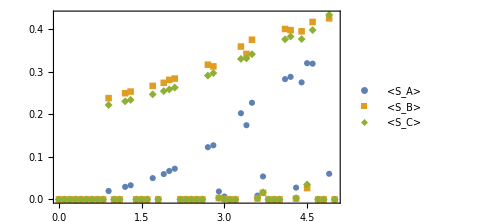

```mathematica
Block[ {bsp={{0.45,0.0},{0.0,0.0},0.6},fil=3.0, β=100, krange=30},DiscretePlot[{Norm[Magn[bsp,U,fil,β,krange,1]],Norm[Magn[bsp,U,fil,β,krange,2]],Norm[Magn[bsp,U,fil,β,krange,3]]},{U,0,5,0.1},PlotRange->All,PlotMarkers->Automatic,Joined->False, PlotLegends->{"<S_A>","<S_B>","<S_C>"}]]
```

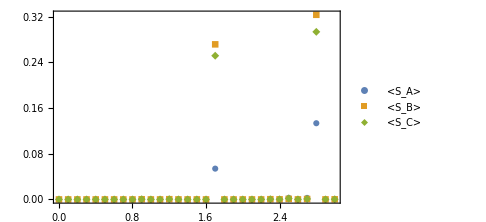

$Aborted

```mathematica
Block[ {bsp={{0.45,0.0},{0.2,0.2},0.6},fil=3.0, β=100, krange=30},DiscretePlot[{Norm[Magn[bsp,U,fil,β,krange,1]],Norm[Magn[bsp,U,fil,β,krange,2]],Norm[Magn[bsp,U,fil,β,krange,3]]},{U,0,3,0.1},PlotRange->All,PlotMarkers->Automatic,Joined->False, PlotLegends->{"<S_A>","<S_B>","<S_C>"}]]
```